```mathematica
(*Exercise 8.2 i) *)
```

```mathematica
data821={{0,4.88},{4.7,6.92},{9.5,8.99},{14.3,11.09},{19.1,13.18},{23.9,15.26},{28.7,17.39},{0,4.95},{4.7,7},{9.5,9.1},{14.3,11.2},{19.1,13.3},{24,15.41},{28.7,17.51}}
model821=LinearModelFit[data821,m,m]
```

{{0,4.88},{4.7,6.92},{9.5,8.99},{14.3,11.09},{19.1,13.18},{23.9,15.26},{28.7,17.39},{0,4.95},{4.7,7},{9.5,9.1},{14.3,11.2},{19.1,13.3},{24,15.41},{28.7,17.51}}

FittedModel[4.90738+0.436293 m]

```mathematica
{{0,4.88},{4.7,6.92},{9.5,8.99},{14.3,11.09},{19.1,13.18},{23.9,15.26},{28.7,17.39},{0,4.95},{4.7,7},{9.5,9.1},{14.3,11.2},{19.1,13.3},{24,15.41},{28.7,17.51}}
```

{{0,4.88},{4.7,6.92},{9.5,8.99},{14.3,11.09},{19.1,13.18},{23.9,15.26},{28.7,17.39},{0,4.95},{4.7,7},{9.5,9.1},{14.3,11.2},{19.1,13.3},{24,15.41},{28.7,17.51}}

4.90738+0.436293 m

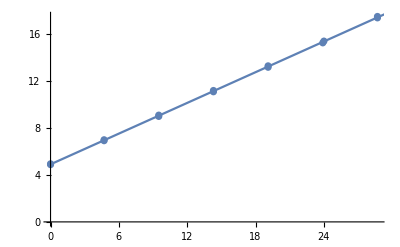

```mathematica
model821["BestFit"]
Show[ListPlot[data821],Plot[model821["BestFit"],{m,0,30}]]
```

```mathematica
Needs["LinearRegression`"]
(* R^2 *)
```

General::obspkg: LinearRegression` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Regress[data821,{1,m^2},m,RegressionReport->{RSquared}]
```

{RSquared→0.924169}

```mathematica
Rsquare=0.924169
```

0.924169

```mathematica
R=Sqrt[Rsquare]
```

0.961337

```mathematica
T12=R*Sqrt[12]/Sqrt[1-R^2]
```

12.0932

```mathematica
halfpvalue=1-CDF[StudentTDistribution,chi12]
```

1-CDF[StudentTDistribution,chi12]

```mathematica
pvalue=2*halfpvalue
```

2 (1-CDF[StudentTDistribution,chi12])

```mathematica
2 (1-CDF[StudentTDistribution[12],12.093247180503433])
```

4.43611×10^-8

Thus significance

```mathematica
a=CDF[StudentTDistribution[40],15.65739454]
pvalue=2*(1-a)
```

1.

0.